```mathematica
Import["/home/justin/Research/Projects/Reaching/git/Mathematica/EllipseFitting/vicon_input.m"]
Import["/home/justin/Research/Projects/Reaching/git/Mathematica/EllipseFitting/datasets.m"]
```

```mathematica
annotations = LoadAnnotations[];
reaches = ExtractReaches[currentDataset, annotations];
planeData = ComputeTrackPlaneData[reaches[[2]], 1]
outConic = ComputeConic2D[planeData[[5,2]]];
outConicParametric = ComputeParametricEllipseFromConic2D[outConic[[1,2]]];
```

{CTPPlaneData→{Plane→{0.000465737,0.00248243,-0.00135168,0.999996},PlaneNormal→{0.162579,0.866563,-0.471844},PlaneNorm→0.00286468,PlaneNormalized→{0.162579,0.866563,-0.471844,349.078}},CTPRotationMatrix→{{0.949954,-0.266749,-0.162579},{-0.266749,-0.421798,-0.866563},{0.162579,0.866563,-0.471844}},CTPOffsetPts2D→{{-95.9083,-95.8747,-95.9452,-95.956,-96.0233,-96.0324,-96.1927,-96.2925,-96.4345,-96.61,-96.9567,-97.2815,-97.6672,-98.3693,-99.2922,-100.461,-102.022,-103.96,-106.147,-108.737,-111.662,-115.037,-118.977,-123.458,-128.627,-134.403,-140.903,-148.53,-155.754,-163.825,-172.433,-181.3,-190.696,-200.369,-210.446,-221.149,-231.774,-242.883,-254.738,-267.463,-280.781,-294.708,-307.797,-320.06,-331.316,-342.466,-353.25,-364.005,-374.472,-384.264,-393.726,-402.466,-409.944,-417.115,-423.197,-428.817,-433.943,-438.411,-442.556,-446.131,-449.575,-452.601,-455.309,-457.622,-459.656,-461.644,-463.199,-464.757,-466.276,-467.725,-469.193,-470.517,-471.822,-473.133,-474.285},{17.3009,17.3264,17.3713,17.4723,17.5604,17.7757,17.6853,17.7009,17.7517,17.7729,17.9705,18.0188,18.1366,18.257,18.3924,18.4607,18.6318,18.7515,18.9433,19.0414,19.2014,19.4171,19.704,20.0947,20.743,21.625,22.5993,23.6041,24.697,25.8966,26.8985,27.8575,28.8613,29.9428,31.0884,32.2672,33.6925,35.3412,37.5195,40.2163,43.1485,46.3424,49.4898,52.0449,54.1559,55.707,57.7183,60.1711,63.0808,66.0038,69.2238,72.1877,74.7497,77.1219,78.78,80.3799,81.8539,83.2369,84.6747,86.1333,87.6121,89.0804,90.5538,92.0071,93.5914,95.2992,97.1427,98.8889,100.783,102.384,104.072,105.687,107.492,109.292,110.984},{-348.314,-348.05,-347.767,-347.563,-347.265,-347.117,-346.809,-346.661,-346.523,-346.404,-346.397,-346.241,-346.144,-346.297,-346.304,-346.527,-346.723,-347.148,-347.48,-347.796,-348.279,-348.6,-349.003,-349.348,-349.913,-350.343,-350.934,-351.425,-351.619,-352.054,-352.38,-352.682,-352.877,-353.027,-353.113,-353.47,-353.679,-353.875,-354.043,-354.242,-354.123,-353.48,-352.724,-351.994,-351.064,-350.323,-349.634,-348.839,-347.883,-346.916,-345.856,-345.058,-344.489,-343.959,-343.726,-343.613,-343.613,-343.757,-344.009,-344.335,-344.731,-345.221,-345.843,-346.622,-347.595,-348.582,-349.846,-350.798,-351.955,-352.721,-353.428,-353.932,-354.36,-354.49,-354.487}},CTPMeanOffset→-349.046,CTPPts2D→{{-95.9083,-95.8747,-95.9452,-95.956,-96.0233,-96.0324,-96.1927,-96.2925,-96.4345,-96.61,-96.9567,-97.2815,-97.6672,-98.3693,-99.2922,-100.461,-102.022,-103.96,-106.147,-108.737,-111.662,-115.037,-118.977,-123.458,-128.627,-134.403,-140.903,-148.53,-155.754,-163.825,-172.433,-181.3,-190.696,-200.369,-210.446,-221.149,-231.774,-242.883,-254.738,-267.463,-280.781,-294.708,-307.797,-320.06,-331.316,-342.466,-353.25,-364.005,-374.472,-384.264,-393.726,-402.466,-409.944,-417.115,-423.197,-428.817,-433.943,-438.411,-442.556,-446.131,-449.575,-452.601,-455.309,-457.622,-459.656,-461.644,-463.199,-464.757,-466.276,-467.725,-469.193,-470.517,-471.822,-473.133,-474.285},{17.3009,17.3264,17.3713,17.4723,17.5604,17.7757,17.6853,17.7009,17.7517,17.7729,17.9705,18.0188,18.1366,18.257,18.3924,18.4607,18.6318,18.7515,18.9433,19.0414,19.2014,19.4171,19.704,20.0947,20.743,21.625,22.5993,23.6041,24.697,25.8966,26.8985,27.8575,28.8613,29.9428,31.0884,32.2672,33.6925,35.3412,37.5195,40.2163,43.1485,46.3424,49.4898,52.0449,54.1559,55.707,57.7183,60.1711,63.0808,66.0038,69.2238,72.1877,74.7497,77.1219,78.78,80.3799,81.8539,83.2369,84.6747,86.1333,87.6121,89.0804,90.5538,92.0071,93.5914,95.2992,97.1427,98.8889,100.783,102.384,104.072,105.687,107.492,109.292,110.984}}}

```mathematica
rxyCPP={{0.6334102,-0.2073607,-0.1433430},{-0.2073607,-0.4329400,-0.7640333},{0.1433430,0.7640333,-0.4718437}};
```

```mathematica
reachesAndConics = AnnotationReachAndConics[currentDataset, annotations, 1];
```

```mathematica
firstReach = reachesAndConics[[2]];
firstReachTrack = firstReach[[1,2,1,2]]
firstReachTrackE = firstReach[[1,2,4,2]]
```

{{-152.352,-283.55,164.95},{-152.284,-283.341,164.798},{-152.317,-283.096,164.637},{-152.321,-282.959,164.455},{-152.36,-282.72,164.249},{-152.402,-282.68,163.994},{-152.48,-282.332,163.953},{-152.555,-282.184,163.886},{-152.681,-282.048,163.8},{-152.834,-281.907,163.754},{-153.215,-281.892,163.636},{-153.511,-281.69,163.573},{-153.893,-281.553,163.488},{-154.617,-281.549,163.57},{-155.531,-281.366,163.606},{-156.696,-281.276,163.842},{-158.256,-281.102,164.04},{-160.198,-281.004,164.452},{-162.381,-280.789,164.798},{-164.919,-280.413,165.283},{-167.819,-280.119,165.848},{-171.134,-279.588,166.361},{-175.019,-279.007,166.943},{-179.436,-278.276,167.496},{-184.611,-277.66,168.041},{-190.404,-276.864,168.419},{-196.934,-276.053,168.91},{-204.527,-274.868,169.511},{-211.713,-273.57,169.83},{-219.771,-272.3,170.308},{-228.268,-270.709,170.993},{-236.996,-269.01,171.746},{-246.222,-267.096,172.496},{-255.723,-265.102,173.202},{-265.616,-262.971,173.888},{-276.155,-260.923,174.775},{-286.663,-258.871,175.366},{-297.688,-256.773,175.836},{-309.558,-254.675,175.955},{-322.398,-252.591,175.781},{-335.812,-250.172,175.349},{-349.789,-247.247,174.542},{-362.94,-244.428,173.586},{-375.152,-241.602,173.021},{-386.257,-238.684,172.583},{-397.142,-235.722,172.702},{-407.811,-233.096,172.387},{-418.553,-230.573,171.635},{-429.116,-228.18,170.364},{-439.041,-225.963,168.967},{-448.716,-223.879,167.215},{-457.68,-222.106,165.691},{-465.374,-220.699,164.418},{-472.733,-219.327,163.278},{-478.915,-218.202,162.72},{-484.662,-217.28,162.194},{-489.925,-216.534,161.75},{-494.561,-216.051,161.346},{-498.924,-215.77,160.893},{-502.762,-215.714,160.364},{-506.492,-215.762,159.829},{-509.838,-215.999,159.28},{-512.905,-216.437,158.737},{-515.616,-217.108,158.221},{-518.129,-218.077,157.638},{-520.634,-219.122,156.947},{-522.808,-220.581,156.199},{-524.909,-221.726,155.388},{-527.045,-223.123,154.54},{-528.973,-224.075,153.749},{-530.933,-225.008,152.859},{-532.703,-225.773,151.912},{-534.494,-226.557,150.762},{-536.241,-227.079,149.477},{-537.786,-227.483,148.197}}

{{-208.752,-139.715,67.8113},{-208.481,-139.403,67.5597},{-208.211,-139.127,67.3204},{-208.018,-138.77,67.1751},{-207.836,-138.45,67.0706},{-207.676,-138.185,66.9823},{-207.586,-137.811,67.0167},{-207.522,-137.496,67.0566},{-207.525,-137.156,67.128},{-207.562,-136.834,67.2213},{-207.64,-136.487,67.3573},{-207.768,-136.066,67.5036},{-207.973,-135.667,67.6939},{-208.221,-135.151,67.9371},{-208.579,-134.508,68.2668},{-208.935,-133.861,68.5442},{-209.365,-133.027,68.8996},{-209.743,-132.172,69.2043},{-210.207,-131.119,69.6078},{-210.658,-129.953,69.9718},{-211.199,-128.589,70.4384},{-211.904,-126.489,71.4069},{-214.291,-123.675,72.7894},{-213.39,-123.523,72.2767},{-215.849,-119.605,74.282},{-216.394,-118.125,74.7533},{-217.948,-114.8,75.9233},{-219.22,-112.327,76.9477},{-220.585,-109.851,78.0253},{-221.998,-107.315,79.2394},{-223.185,-105.595,79.9536},{-224.755,-103.348,81.7904},{-226.353,-101.292,83.0954},{-228.135,-99.7372,84.2709},{-229.944,-97.9845,86.0688},{-232.171,-96.279,88.1606},{-233.927,-95.6709,89.8489},{-236.446,-95.0273,91.8153},{-239.747,-94.172,94.2001},{-242.162,-94.5042,96.5893},{-245.562,-94.6785,99.1737},{-249.211,-95.032,101.817},{-252.933,-95.7021,104.579},{-257.002,-96.3415,107.477},{-261.216,-97.5491,109.703},{-265.121,-98.4404,112.435},{-269.078,-99.0644,115.112},{-272.99,-99.6105,117.913},{-276.885,-100.202,120.839},{-280.737,-100.942,123.843},{-284.922,-101.681,126.919},{-288.802,-102.885,129.987},{-292.768,-104.24,133.015},{-296.335,-105.976,135.881},{-299.791,-107.544,138.686},{-302.853,-109.09,141.263},{-305.933,-110.164,143.68},{-308.46,-111.298,145.845},{-310.781,-112.022,148.256},{-313.477,-113.076,149.841},{-315.804,-114.033,151.661},{-317.882,-115.226,153.35},{-320.041,-116.044,155.452},{-321.768,-117.949,156.655},{-323.376,-119.544,158.382},{-325.099,-121.013,160.378},{-326.587,-122.886,162.095},{-327.831,-125.262,163.403},{-329.217,-127.226,164.999},{-330.674,-128.767,166.686},{-331.876,-130.548,167.766},{-333.049,-132.093,168.671},{-334.094,-133.568,169.245},{-335.146,-134.903,169.576},{-336.224,-135.775,170.022}}

```mathematica
Show[
{
ListPointPlot3D[firstReachTrack
(*, PlotRange->{{-300,300},{-300,300},{-300,300}}*)
, AspectRatio->1]
(*ListPointPlot3D[firstReachTrackE]*)
}]
```

-Graphics3D-

```mathematica
firstReachTrack
```

{{-152.352,-283.55,164.95},{-152.284,-283.341,164.798},{-152.317,-283.096,164.637},{-152.321,-282.959,164.455},{-152.36,-282.72,164.249},{-152.402,-282.68,163.994},{-152.48,-282.332,163.953},{-152.555,-282.184,163.886},{-152.681,-282.048,163.8},{-152.834,-281.907,163.754},{-153.215,-281.892,163.636},{-153.511,-281.69,163.573},{-153.893,-281.553,163.488},{-154.617,-281.549,163.57},{-155.531,-281.366,163.606},{-156.696,-281.276,163.842},{-158.256,-281.102,164.04},{-160.198,-281.004,164.452},{-162.381,-280.789,164.798},{-164.919,-280.413,165.283},{-167.819,-280.119,165.848},{-171.134,-279.588,166.361},{-175.019,-279.007,166.943},{-179.436,-278.276,167.496},{-184.611,-277.66,168.041},{-190.404,-276.864,168.419},{-196.934,-276.053,168.91},{-204.527,-274.868,169.511},{-211.713,-273.57,169.83},{-219.771,-272.3,170.308},{-228.268,-270.709,170.993},{-236.996,-269.01,171.746},{-246.222,-267.096,172.496},{-255.723,-265.102,173.202},{-265.616,-262.971,173.888},{-276.155,-260.923,174.775},{-286.663,-258.871,175.366},{-297.688,-256.773,175.836},{-309.558,-254.675,175.955},{-322.398,-252.591,175.781},{-335.812,-250.172,175.349},{-349.789,-247.247,174.542},{-362.94,-244.428,173.586},{-375.152,-241.602,173.021},{-386.257,-238.684,172.583},{-397.142,-235.722,172.702},{-407.811,-233.096,172.387},{-418.553,-230.573,171.635},{-429.116,-228.18,170.364},{-439.041,-225.963,168.967},{-448.716,-223.879,167.215},{-457.68,-222.106,165.691},{-465.374,-220.699,164.418},{-472.733,-219.327,163.278},{-478.915,-218.202,162.72},{-484.662,-217.28,162.194},{-489.925,-216.534,161.75},{-494.561,-216.051,161.346},{-498.924,-215.77,160.893},{-502.762,-215.714,160.364},{-506.492,-215.762,159.829},{-509.838,-215.999,159.28},{-512.905,-216.437,158.737},{-515.616,-217.108,158.221},{-518.129,-218.077,157.638},{-520.634,-219.122,156.947},{-522.808,-220.581,156.199},{-524.909,-221.726,155.388},{-527.045,-223.123,154.54},{-528.973,-224.075,153.749},{-530.933,-225.008,152.859},{-532.703,-225.773,151.912},{-534.494,-226.557,150.762},{-536.241,-227.079,149.477},{-537.786,-227.483,148.197}}

```mathematica
ptsTwo={{-248.2987610,-230.6821580,-213.1569271,-195.7922323,-178.6566043,-161.8176695,-145.3418835,-129.2942686,-113.7381576,-98.7349432,-84.3438362,-70.6216319,-57.6224855,-45.3976986,-33.9955169,-23.4609397,-13.8355421,-5.1573111,2.5395043,9.2245282,14.8713779,19.4577679,22.9655978,25.3810237,26.6945132,26.9008824,25.9993169,23.9933748,20.8909726,16.7043540,11.4500419,5.1487724,-2.1745861,-10.4911317,-19.7680427,-29.9687076,-41.0528689,-52.9767824,-65.6933899,-79.1525049,-93.3010103,-108.0830684,-123.4403412,-139.3122206,-155.6360675,-172.3474592,-189.3804433,-206.6677986,-224.1412996,-241.7319866,-259.3704370,-276.9870400,-294.5122709,-311.8769657,-329.0125937,-345.8515285,-362.3273145,-378.3749294,-393.9310404,-408.9342549,-423.3253618,-437.0475661,-450.0467125,-462.2714994,-473.6736811,-484.2082583,-493.8336559,-502.5118870,-510.2087023,-516.8937262,-522.5405759,-527.1269659,-530.6347958,-533.0502217,-534.3637112,-534.5700804,-533.6685149,-531.6625728,-528.5601706,-524.3735521,-519.1192399,-512.8179704,-505.4946119,-497.1780663,-487.9011553,-477.7004904,-466.6163292,-454.6924156,-441.9758081,-428.5166931,-414.3681877,-399.5861296,-384.2288568,-368.3569774,-352.0331305,-335.3217388,-318.2887547,-301.0013994,-283.5278984,-265.9372114},{-263.0635559,-266.8239955,-270.6435794,-274.5072335,-278.3997098,-282.3056464,-286.2096283,-290.0962484,-293.9501680,-297.7561773,-301.4992558,-305.1646313,-308.7378382,-312.2047746,-315.5517583,-318.7655801,-321.8335566,-324.7435798,-327.4841653,-330.0444972,-332.4144711,-334.5847336,-336.5467199,-338.2926869,-339.8157439,-341.1098802,-342.1699885,-342.9918849,-343.5723258,-343.9090205,-344.0006403,-343.8468234,-343.4481770,-342.8062744,-341.9236488,-340.8037835,-339.4510982,-337.8709313,-336.0695190,-334.0539706,-331.8322405,-329.4130971,-326.8060874,-324.0215002,-321.0703249,-317.9642085,-314.7154095,-311.3367493,-307.8415620,-304.2436414,-300.5571870,-296.7967475,-292.9771636,-289.1135095,-285.2210332,-281.3150966,-277.4111146,-273.5244945,-269.6705750,-265.8645657,-262.1214872,-258.4561117,-254.8829048,-251.4159683,-248.0689847,-244.8551629,-241.7871864,-238.8771631,-236.1365776,-233.5762457,-231.2062719,-229.0360093,-227.0740230,-225.3280561,-223.8049991,-222.5108628,-221.4507545,-220.6288581,-220.0484172,-219.7117224,-219.6201027,-219.7739196,-220.1725660,-220.8144686,-221.6970942,-222.8169595,-224.1696448,-225.7498117,-227.5512240,-229.5667724,-231.7885024,-234.2076459,-236.8146556,-239.5992428,-242.5504181,-245.6565345,-248.9053335,-252.2839937,-255.7791810,-259.3771015},{171.1336475,170.2974218,169.3210914,168.2085094,166.9640667,165.5926746,164.0997451,162.4911704,160.7732987,158.9529096,157.0371874,155.0336926,152.9503320,150.7953277,148.5771846,146.3046566,143.9867124,141.6324998,139.2513099,136.8525400,134.4456572,132.0401601,129.6455422,127.2712541,124.9266658,122.6210305,120.3634474,118.1628261,116.0278516,113.9669496,111.9882535,110.0995723,108.3083598,106.6216851,105.0462047,103.5881364,102.2532344,101.0467670,99.9734956,99.0376559,98.2429412,97.5924879,97.0888631,96.7340543,96.5294617,96.4758929,96.5735592,96.8220752,97.2204602,97.7671417,98.4599625,99.2961881,100.2725185,101.3851005,102.6295432,104.0009354,105.4938648,107.1024395,108.8203113,110.6407004,112.5564226,114.5599174,116.6432780,118.7982822,121.0164253,123.2889533,125.6068975,127.9611101,130.3423001,132.7410699,135.1479528,137.5534498,139.9480677,142.3223559,144.6669441,146.9725794,149.2301626,151.4307838,153.5657583,155.6266604,157.6053565,159.4940377,161.2852501,162.9719248,164.5474052,166.0054736,167.3403756,168.5468429,169.6201143,170.5559540,171.3506687,172.0011220,172.5047469,172.8595557,173.0641482,173.1177170,173.0200507,172.7715347,172.3731498,171.8264682},{1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000}};
ptsXY={{-95.9082688,-95.8747104,-95.9452371,-95.9559921,-96.0233019,-96.0324123,-96.1926715,-96.2925041,-96.4344944,-96.6099703,-96.9567198,-97.2815471,-97.6671550,-98.3693204,-99.2922465,-100.4613193,-102.0218529,-103.9597881,-106.1471417,-108.7372741,-111.6624229,-115.0365681,-118.9767426,-123.4575903,-128.6265266,-134.4033988,-140.9027600,-148.5295703,-155.7540445,-163.8252600,-172.4327856,-181.2996149,-190.6963846,-200.3685783,-210.4464470,-221.1485244,-231.7740968,-242.8833941,-254.7383374,-267.4633663,-280.7810845,-294.7076345,-307.7970227,-320.0598394,-331.3162451,-342.4659543,-353.2502866,-364.0054433,-374.4715024,-384.2640579,-393.7259316,-402.4664971,-409.9437979,-417.1151508,-423.1971415,-428.8169547,-433.9433737,-438.4105196,-442.5564784,-446.1313366,-449.5748825,-452.6009544,-455.3093479,-457.6217950,-459.6557671,-461.6443082,-463.1987135,-464.7572887,-466.2758762,-467.7248434,-469.1931821,-470.5165761,-471.8218475,-473.1332608,-474.2850726},{17.3009342,17.3263571,17.3713359,17.4723311,17.5604366,17.7757417,17.6852915,17.7009312,17.7517015,17.7729024,17.9704611,18.0188090,18.1365785,18.2569592,18.3923821,18.4606736,18.6318292,18.7514949,18.9432898,19.0414188,19.2013731,19.4171234,19.7040376,20.0947227,20.7430425,21.6250055,22.5993136,23.6041011,24.6970296,25.8965897,26.8984767,27.8575022,28.8612817,29.9428020,31.0884327,32.2672130,33.6925397,35.3412268,37.5194802,40.2162880,43.1484805,46.3423838,49.4897812,52.0449228,54.1559148,55.7069873,57.7182546,60.1711278,63.0808330,66.0037759,69.2237607,72.1876900,74.7497193,77.1218977,78.7799574,80.3798764,81.8538673,83.2368772,84.6747294,86.1333020,87.6121321,89.0803824,90.5537918,92.0071204,93.5913884,95.2991678,97.1426719,98.8888522,100.7827246,102.3840192,104.0716252,105.6870811,107.4920651,109.2917872,110.9835210},{-348.3138219,-348.0499346,-347.7670250,-347.5630806,-347.2651128,-347.1169584,-346.8087301,-346.6610586,-346.5231124,-346.4040968,-346.3973634,-346.2407149,-346.1439943,-346.2969264,-346.3039290,-346.5266980,-346.7229643,-347.1481692,-347.4800261,-347.7956682,-348.2789695,-348.5998298,-349.0025892,-349.3481728,-349.9128712,-350.3432642,-350.9337979,-351.4249613,-351.6189735,-352.0540415,-352.3799866,-352.6819840,-352.8772192,-353.0270774,-353.1125106,-353.4697352,-353.6787878,-353.8749388,-354.0428520,-354.2423485,-354.1231311,-353.4800233,-352.7241763,-351.9940925,-351.0642340,-350.3232963,-349.6336266,-348.8388854,-347.8828090,-346.9160699,-345.8564344,-345.0582867,-344.4892585,-343.9588513,-343.7257426,-343.6129234,-343.6126222,-343.7571637,-344.0092467,-344.3350921,-344.7306706,-345.2209933,-345.8429667,-346.6217110,-347.5948869,-348.5816618,-349.8464851,-350.7976132,-351.9553472,-352.7205393,-353.4277566,-353.9316063,-354.3595506,-354.4896030,-354.4869192}};
planeCPP={{0.1625790},{0.8665631},{-0.4718437},{349.0776723}};
rxyCPP={{0.9499543,-0.2667487,-0.1625790},{-0.2667487,-0.4217980,-0.8665631},{0.1625790,0.8665631,-0.4718437}};
```

```mathematica
Show[{ListPointPlot3D[firstReachTrack], ListPointPlot3D[Transpose[HomToCart3D[ptsTwo]], PlotStyle->Red]}]
```

-Graphics3D-

```mathematica
normalToPlane = planeData[[1,2,2,2]];
zAxis = {0,0,1};
Cross[normalToPlane,zAxis]

CrossProductMatrix[inVect_]:= {{0, -inVect[[3]], inVect[[2]]},{inVect[[3]],0,-inVect[[1]]},{-inVect[[2]], inVect[[1]],0}}

RotMatBetweenTwoVecs[inVectA_, inVectB_]:= (
vectV = Cross[inVectA, inVectB];
vectV = vectV / Norm[vectV];
crossProductMatrix = CrossProductMatrix[vectV];
IdentityMatrix[3] +
  crossProductMatrix+
((crossProductMatrix * Transpose[crossProductMatrix])*
(1 / (1+inVectA.inVectB)))
)

rotMat = RotMatBetweenTwoVecs[normalToPlane, zAxis]
rotMat.normalToPlane
```

{0.866563,-0.162579,0.}

{{1.,0.,-0.248775},{0.,1.,-2.81185},{0.120018,-0.846148,1.}}

{0.279962,2.19332,-1.18557}

```mathematica
rotMat.Transpose[rotMat]
```

{{1.06189,0.699519,-0.128757},{0.699519,8.90651,-3.658},{-0.128757,-3.658,1.73037}}

```mathematica
{{cos[alpha], -sin[alpha], cX},{sin[alpha], cos[alpha], cY},{0,0,1}}.Transpose[{{a * cos[theta], b * sin[theta], 1}}]
```

{{cX+a cos[alpha] cos[theta]-b sin[alpha] sin[theta]},{cY+a cos[theta] sin[alpha]+b cos[alpha] sin[theta]},{1}}

```mathematica
{{1,0,0},{0,1,0},{0,0,1}}.{a,b,c}
```

{a,b,c}

```mathematica
inPts={{-95.9082688,-95.8747104,-95.9452371,-95.9559921,-96.0233019,-96.0324123,-96.1926715,-96.2925041,-96.4344944,-96.6099703,-96.9567198,-97.2815471,-97.6671550,-98.3693204,-99.2922465,-100.4613193,-102.0218529,-103.9597881,-106.1471417,-108.7372741,-111.6624229,-115.0365681,-118.9767426,-123.4575903,-128.6265266,-134.4033988,-140.9027600,-148.5295703,-155.7540445,-163.8252600,-172.4327856,-181.2996149,-190.6963846,-200.3685783,-210.4464470,-221.1485244,-231.7740968,-242.8833941,-254.7383374,-267.4633663,-280.7810845,-294.7076345,-307.7970227,-320.0598394,-331.3162451,-342.4659543,-353.2502866,-364.0054433,-374.4715024,-384.2640579,-393.7259316,-402.4664971,-409.9437979,-417.1151508,-423.1971415,-428.8169547,-433.9433737,-438.4105196,-442.5564784,-446.1313366,-449.5748825,-452.6009544,-455.3093479,-457.6217950,-459.6557671,-461.6443082,-463.1987135,-464.7572887,-466.2758762,-467.7248434,-469.1931821,-470.5165761,-471.8218475,-473.1332608,-474.2850726},{17.3009342,17.3263571,17.3713359,17.4723311,17.5604366,17.7757417,17.6852915,17.7009312,17.7517015,17.7729024,17.9704611,18.0188090,18.1365785,18.2569592,18.3923821,18.4606736,18.6318292,18.7514949,18.9432898,19.0414188,19.2013731,19.4171234,19.7040376,20.0947227,20.7430425,21.6250055,22.5993136,23.6041011,24.6970296,25.8965897,26.8984767,27.8575022,28.8612817,29.9428020,31.0884327,32.2672130,33.6925397,35.3412268,37.5194802,40.2162880,43.1484805,46.3423838,49.4897812,52.0449228,54.1559148,55.7069873,57.7182546,60.1711278,63.0808330,66.0037759,69.2237607,72.1876900,74.7497193,77.1218977,78.7799574,80.3798764,81.8538673,83.2368772,84.6747294,86.1333020,87.6121321,89.0803824,90.5537918,92.0071204,93.5913884,95.2991678,97.1426719,98.8888522,100.7827246,102.3840192,104.0716252,105.6870811,107.4920651,109.2917872,110.9835210},{-348.3138219,-348.0499346,-347.7670250,-347.5630806,-347.2651128,-347.1169584,-346.8087301,-346.6610586,-346.5231124,-346.4040968,-346.3973634,-346.2407149,-346.1439943,-346.2969264,-346.3039290,-346.5266980,-346.7229643,-347.1481692,-347.4800261,-347.7956682,-348.2789695,-348.5998298,-349.0025892,-349.3481728,-349.9128712,-350.3432642,-350.9337979,-351.4249613,-351.6189735,-352.0540415,-352.3799866,-352.6819840,-352.8772192,-353.0270774,-353.1125106,-353.4697352,-353.6787878,-353.8749388,-354.0428520,-354.2423485,-354.1231311,-353.4800233,-352.7241763,-351.9940925,-351.0642340,-350.3232963,-349.6336266,-348.8388854,-347.8828090,-346.9160699,-345.8564344,-345.0582867,-344.4892585,-343.9588513,-343.7257426,-343.6129234,-343.6126222,-343.7571637,-344.0092467,-344.3350921,-344.7306706,-345.2209933,-345.8429667,-346.6217110,-347.5948869,-348.5816618,-349.8464851,-350.7976132,-351.9553472,-352.7205393,-353.4277566,-353.9316063,-354.3595506,-354.4896030,-354.4869192}};
outPts={{-95.8563208,-95.8251697,-95.8984218,-95.9185536,-95.9927797,-96.0199485,-96.1714009,-96.2716935,-96.4169194,-96.5929032,-96.9539578,-97.2805433,-97.6732998,-98.3807659,-99.3083485,-100.4748248,-102.0382041,-103.9715540,-106.1585054,-108.7358669,-111.6502754,-115.0140426,-118.9438006,-123.4181311,-128.5980134,-134.4030151,-140.9313315,-148.5757946,-155.8305981,-163.9321613,-172.5335519,-181.3794803,-190.7443673,-200.3806461,-210.4146753,-221.0528548,-231.6398012,-242.7223588,-254.6029521,-267.4051726,-280.8120170,-294.8425589,-308.0423190,-320.3167469,-331.5148195,-342.4641130,-353.1278509,-363.8350501,-374.3497586,-384.2121001,-393.8195194,-402.6697153,-410.2231298,-417.4179695,-423.3785382,-428.8694371,-433.8424457,-438.1699089,-442.2008480,-445.7207397,-449.1029017,-452.1040526,-454.8208569,-457.1904314,-459.3810813,-461.5689157,-463.4972323,-465.3675076,-467.2593914,-468.9016621,-470.4698362,-471.6662726,-472.3551610,-472.3454077,-472.0847813},{17.9084861,17.9058292,17.9120777,17.9137956,17.9201314,17.9224513,17.9353919,17.9439689,17.9563994,17.9714797,18.0024777,18.0305842,18.0644708,18.1257448,18.2065391,18.3088733,18.4473005,18.6204915,18.8190559,19.0566595,19.3299782,19.6515094,20.0352984,20.4828564,21.0149011,21.6286765,22.3407768,23.2036528,24.0511710,25.0302194,26.1070187,27.2543061,28.5128056,29.8548876,31.3032932,32.8960323,34.5401128,36.3252252,38.3132247,40.5440363,42.9824525,45.6517845,48.2792297,50.8304174,53.2552998,55.7233444,58.2272767,60.8507222,63.5454459,66.1929299,68.8991011,71.5197961,73.8689609,76.2190778,78.2631703,80.2376355,82.1148134,83.8294896,85.5072337,87.0478163,88.6077103,90.0707965,91.4734214,92.7712574,94.0476284,95.4151550,96.7202308,98.1065787,99.6822978,101.2723573,103.1480030,105.1531410,107.4195552,109.1715779,110.2267438},{1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000}};
fixedThetas={{3.4907598,0.3492828,0.3490108,0.3489360,0.3486603,0.3485595,0.3479971,0.3476248,0.3470858,0.3464327,0.3450933,0.3438823,0.3424265,0.3398061,0.3363738,0.3320630,0.3262949,0.3191762,0.3111425,0.3016993,0.2910523,0.2788026,0.2645418,0.2483661,0.2297152,0.2089008,0.1855911,0.1584102,0.1327101,0.1040977,0.0737951,0.0426824,0.0097678,-0.0241124,-0.0594454,-0.0970156,-0.1345700,-0.1741202,-0.2168645,-0.2634263,-0.3128759,-0.3655506,-0.4161536,-0.4643024,-0.5093160,-0.5545062,-0.5998264,-0.6468575,-0.6948031,-0.7416617,-0.7894167,-0.8356290,-0.8771065,-0.9187262,-0.9550858,-0.9903976,-1.0241876,-1.0552756,-1.0859353,-1.1143289,-1.1433438,-1.1708298,-1.1974544,-1.2223539,-1.2471128,-1.2739669,-1.2999398,-1.3279360,-1.3603171,-1.3936670,-1.4339917,-1.4784556,-1.5307016,-1.5728069,-1.5990078}};
speed={{-3.1414770,-0.0002721,-0.0000748,-0.0002756,-0.0001009,-0.0005623,-0.0003723,-0.0005390,-0.0006531,-0.0013394,-0.0012110,-0.0014557,-0.0026204,-0.0034323,-0.0043108,-0.0057682,-0.0071187,-0.0080337,-0.0094431,-0.0106471,-0.0122497,-0.0142608,-0.0161756,-0.0186509,-0.0208144,-0.0233097,-0.0271809,-0.0257001,-0.0286123,-0.0303026,-0.0311127,-0.0329146,-0.0338802,-0.0353330,-0.0375701,-0.0375545,-0.0395502,-0.0427442,-0.0465618,-0.0494496,-0.0526747,-0.0506031,-0.0481488,-0.0450135,-0.0451903,-0.0453202,-0.0470310,-0.0479457,-0.0468585,-0.0477550,-0.0462123,-0.0414776,-0.0416197,-0.0363596,-0.0353118,-0.0337899,-0.0310881,-0.0306596,-0.0283936,-0.0290149,-0.0274860,-0.0266247,-0.0248995,-0.0247589,-0.0268540,-0.0259730,-0.0279961,-0.0323811,-0.0333499,-0.0403247,-0.0444638,-0.0522460,-0.0421053,-0.0262008}};
acceleration={{3.1412049,0.0001973,-0.0002009,0.0001748,-0.0004614,0.0001900,-0.0001667,-0.0001140,-0.0006863,0.0001284,-0.0002447,-0.0011647,-0.0008119,-0.0008785,-0.0014574,-0.0013505,-0.0009150,-0.0014094,-0.0012039,-0.0016026,-0.0020111,-0.0019148,-0.0024753,-0.0021635,-0.0024954,-0.0038711,0.0014808,-0.0029122,-0.0016903,-0.0008101,-0.0018018,-0.0009656,-0.0014528,-0.0022371,0.0000157,-0.0019957,-0.0031940,-0.0038176,-0.0028878,-0.0032251,0.0020716,0.0024543,0.0031352,-0.0001767,-0.0001299,-0.0017109,-0.0009146,0.0010872,-0.0008965,0.0015427,0.0047347,-0.0001421,0.0052601,0.0010477,0.0015219,0.0027019,0.0004284,0.0022660,-0.0006213,0.0015290,0.0008613,0.0017252,0.0001405,-0.0020951,0.0008810,-0.0020232,-0.0043850,-0.0009688,-0.0069748,-0.0041391,-0.0077822,0.0101407,0.0159045}};
jerk={{-3.1410076,-0.0003982,0.0003756,-0.0006362,0.0006515,-0.0003567,0.0000527,-0.0005723,0.0008147,-0.0003731,-0.0009200,0.0003528,-0.0000666,-0.0005789,0.0001069,0.0004355,-0.0004944,0.0002055,-0.0003987,-0.0004085,0.0000963,-0.0005605,0.0003118,-0.0003319,-0.0013758,0.0053519,-0.0043930,0.0012219,0.0008801,-0.0009917,0.0008362,-0.0004872,-0.0007843,0.0022528,-0.0020114,-0.0011983,-0.0006235,0.0009297,-0.0003373,0.0052967,0.0003827,0.0006809,-0.0033120,0.0000468,-0.0015810,0.0007962,0.0020018,-0.0019837,0.0024393,0.0031920,-0.0048768,0.0054022,-0.0042124,0.0004742,0.0011800,-0.0022735,0.0018376,-0.0028874,0.0021503,-0.0006677,0.0008639,-0.0015846,-0.0022356,0.0029761,-0.0029042,-0.0023619,0.0034162,-0.0060060,0.0028356,-0.0036431,0.0179229,0.0057638}};
```

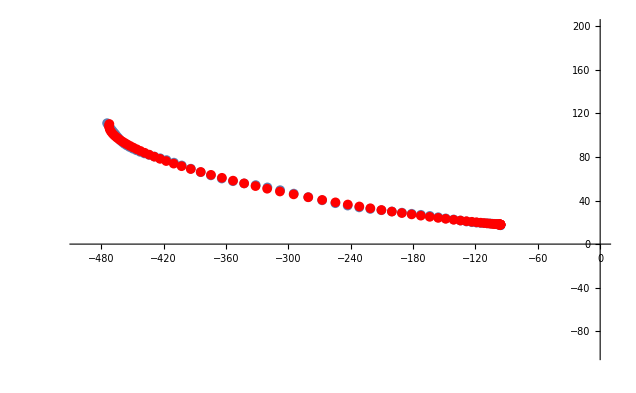

```mathematica
Show[{
ListPlot[Transpose[{inPts[[1]],inPts[[2]]}], PlotRange->{{-500,0}, {-100,200}}],
ListPlot[Transpose[HomToCart2D[outPts]], PlotStyle->Red]
}]
```

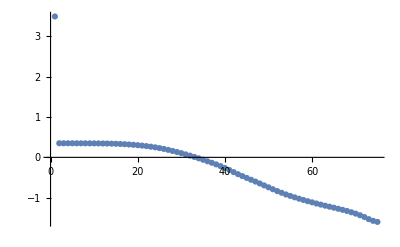

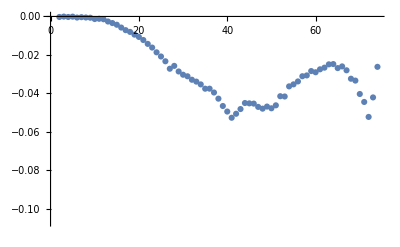

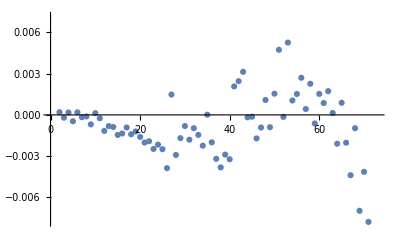

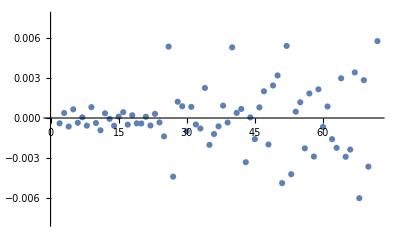

```mathematica
ListPlot[fixedThetas[[1]]]
ListPlot[speed[[1]]]
ListPlot[acceleration[[1]]]
ListPlot[jerk[[1]]]
```